# Muon Beam Dump: BSM Scalar with FeynCalc

#### Notebook Description:

In this notebook, we go through calculations of cross sections for the production of beyond the Standard Model (BSM) states in a muon beam dump experiment, through scattering of the form
μ^-N → μ^- N ϕ_BSM
where ϕ_BSM indicates a BSM scalar.

We set up the relevant definitions and typesetting in Setup and perform calculations in Beam Dump Calculations.

Details:

In Beam Dump Calculations, we calculate cross sections both for the full/complicated 2→3 process. Our calculations use FeynCalc, and rely on a model we design in the format of FeynRules and load using FeynArts.

# Setup

Setting up directories

```mathematica
$DirectorySetup="/Users/sam/Documents/Research/BeamDumpBSM/setup/directories.m";
Get[$DirectorySetup]
```

### FeynCalc, Models, Typesetting

#### Loading FeynCalc and FeynArts

```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True];
```

Patched 1 FeynArts models.

#### Initializing and Typesetting Model

Nuclide Specific Typesetting

```mathematica
MakeBoxes[FFnuclidefermion,TraditionalForm]:=" \!\(\*SubscriptBox[\(F\), fermion]\)(q) ";
MakeBoxes[FFnuclidescalar,TraditionalForm]:=" \!\(\*SubscriptBox[\(F\), scalar]\)(q) ";
```

Model Independent

```mathematica
MakeBoxes[epsel,TraditionalForm]:="\!\(\*SubscriptBox[\(ϵ\), e]\)";
MakeBoxes[epsmu,TraditionalForm]:="\!\(\*SubscriptBox[\(ϵ\), \(μ\)]\)";
```

Model Specific

```mathematica
InitializeModel["scalar_mubeamdump"];
```

loading generic model file /Users/sam/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/sam/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/scalar_mubeamdump.mod

> 14 particles (incl. antiparticles) in 8 classes

> $CounterTerms are ON

> 7 vertices

classes model {scalar_mubeamdump} initialized

Names, couplings, etc

```mathematica
MakeBoxes[mBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(X\)]\)";

MakeBoxes[gel,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), e]\)";
MakeBoxes[gmu,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), \(μ\)]\)";
```

Kinematic Properties of the BSM final state:

```mathematica
MakeBoxes[EBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(E\), \(X\)]\)";
MakeBoxes[betaBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(β\), \(X\)]\)";
MakeBoxes[thetaBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(θ\), \(X\)]\)";
```

#### Other Typesetting

Outgoing lepton:

```mathematica
MakeBoxes[pprime,TraditionalForm]:="\!\(\*p'\)";
```

Beam and Target:

```mathematica
MakeBoxes[E0,TraditionalForm]:="\!\(\*SubscriptBox[\(E\), \(0\)]\)";
MakeBoxes[mTar,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(T\)]\)";
```

SM Parameters:

```mathematica
MakeBoxes[mu,TraditionalForm]:="\!\(\*SubscriptBox[\(μ\)]\)";

MakeBoxes[mel,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), e]\)";
MakeBoxes[mmu,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(μ\)]\)";

MakeBoxes[alphaEM,TraditionalForm]:="\!\(\*SubscriptBox[\(α\), EM]\)";
```

#### Replacement Rules

```mathematica
BeamDumpCouplingRules = {gel->epsel e,gmu->epsmu e,e^2->4π alphaEM};
```

### 2→2 Kinematics

#### Typesetting

We denote the Mandelstam invariants for the effective 2 -> 2 process that emerges due to Weiszäcker-Williams (WW) with a subscript 2 :

```mathematica
MakeBoxes[s2,TraditionalForm]:="\!\(\*SubscriptBox[\(s\), \(2\)]\)";
MakeBoxes[t2,TraditionalForm]:="\!\(\*SubscriptBox[\(t\), \(2\)]\)";
MakeBoxes[u2,TraditionalForm]:="\!\(\*SubscriptBox[\(u\), \(2\)]\)";
```

They have counterparts with a tilde:

```mathematica
MakeBoxes[stilde,TraditionalForm]:="\!\(\*OverscriptBox[\(s\), \(~\)]\)";
MakeBoxes[ttilde,TraditionalForm]:="\!\(\*OverscriptBox[\(t\), \(~\)]\)";
MakeBoxes[utilde,TraditionalForm]:="\!\(\*OverscriptBox[\(u\), \(~\)]\)";
```

Furthermore, there are beam-related kinematic variables of interest:

#### Mandelstam and Kinematic Variable Setup

t (with no subscript) denotes the “momentum transfer” mediated by the intermediate WW photon:

```mathematica
t=-SP[q,q];
```

Mandelstam Setup with awesome built-in FeynCalc functions

```mathematica
SetMandelstam[s2, t2, u2,
p (* Incoming Lepton *),
q (* "Incoming" off-shell photon*),
-1*pprime (* Outgoing Lepton *),
-1*k (* Outgoing BSM Final State *),
 mmu (*Lepton*), q (*photon*), mmu (*Lepton*), mBSM (*BSM*)];
```

Replacements Involving 2 -> 2 Mandelstams :

```mathematica
TwoToTildeEl = {s2->stilde+mel^2,u2->utilde+mel^2};
TwoToTildeMu = {s2->stilde+mmu^2,u2->utilde+mmu^2};
```

```mathematica
TildeToTwoEl = {stilde->s2-mel^2,utilde->u2-mel^2};
TildeToTwoMu = {stilde->s2-mmu^2,utilde->u2-mmu^2};
```

#### Tests

Basics

```mathematica
SP[p,p]
SP[pprime,pprime]
SP[q,q]
SP[k,k]
```

m_μ^2

m_μ^2

q^2

m_X^2

Mandelstams

```mathematica
(* Subscript[s, 2] and s tilde*)
SP[pprime,pprime] + 2SP[pprime,k] + SP[k,k]//FullSimplify
SP[pprime,pprime] + 2SP[pprime,k] + SP[k,k]-mmu^2/.TwoToTildeMu//FullSimplify
```

s_2

s̃

```mathematica
(* Subscript[u, 2] and u tilde*)
SP[p,p] - 2SP[p,k] + SP[k,k]//FullSimplify
SP[p,p] - 2SP[p,k] + SP[k,k]-mmu^2/.TwoToTildeMu//FullSimplify
```

u_2

ũ

```mathematica
(* Subscript[t, 2] *)
SP[pprime,pprime] - 2SP[pprime,p] + SP[p,p]//FullSimplify
```

t_2

#### “Limit Checker” Replacement Rules:

```mathematica
AllMassless = {mel->0,mmu->0,mBSM ->0,
(* also, zero virtuality for the WW photon: *)
SP[q,q]->0,SP[q,q]^2->0};
```

```mathematica
mmu//.AllMassless
```

0

# Beam Dump Calculations

## 2→3 Calculation

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

in total: 1 Classes insertion

> Top. 1 ad/bdcd/0.m, 0 diagrams

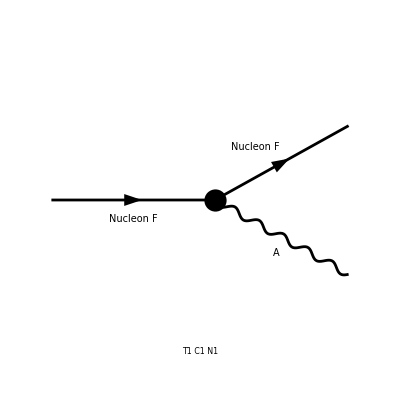

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

e  F_fermion(q)  (φ(OverBar[p'],Mi)).(γ̄·(ε̄)^*(q)).(φ(p̄,Mi))

```mathematica
diagramsFermionicNuclide= InsertFields[CreateTopologies[0, 1 -> 2], {F[9]} ->
		{F[9],V[1]}, InsertionLevel -> {Classes}, Model->{"scalar_mubeamdump"}];
Paint[diagramsFermionicNuclide, SheetHeader->None,ImageSize->{512,256}];
FermionicTestAmplitude = FCFAConvert[CreateFeynAmp[diagramsFermionicNuclide], IncomingMomenta->{p},
	OutgoingMomenta->{pprime, q},UndoChiralSplittings->True,ChangeDimension->4,
	TransversePolarizationVectors->{q}, List->False, SMP->True,
	Contract->True]
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

in total: 1 Classes insertion

> Top. 1 ad/bdcd/0.m, 0 diagrams

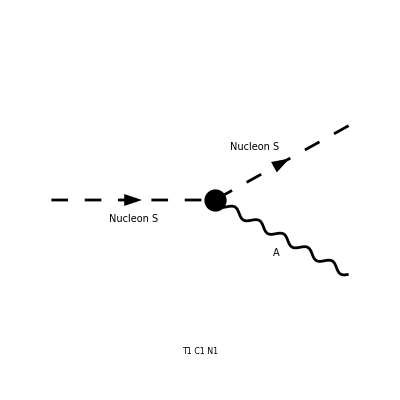

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

e  F_scalar(q)  (OverBar[p']·(ε̄)^*(q)+p̄·(ε̄)^*(q))

```mathematica
diagramsScalarNuclide= InsertFields[CreateTopologies[0, 1 -> 2], {S[9]} ->
		{S[9], V[1]}, InsertionLevel -> {Classes}, Model->{"scalar_mubeamdump"}];
Paint[diagramsScalarNuclide, SheetHeader->None,ImageSize->{512,256}];
ScalarTestAmplitude = FCFAConvert[CreateFeynAmp[diagramsScalarNuclide], IncomingMomenta->{p},
	OutgoingMomenta->{pprime, q},UndoChiralSplittings->True,ChangeDimension->4,
	TransversePolarizationVectors->{q}, List->False, SMP->True,
	Contract->True]
```